### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/Tutorial

### Keywords

# Quantum Computation

Quantum computation is the use of quantum mechanical systems to perform computations. Wolfram quantum framework aims to simulate a wide range of quantum computations in the Wolfram Mathematica.

## Basic quantum objects

QuantumBasis | basis vectors encoding quantum states and operators
QuantumState | quantum discrete state, defined by an association, a complex vector, or a density matrix
QuantumOperator | quantum discrete operator, defined by an association or a matrix representation
QuantumMeasurementOperator | quantum measurement operator, defined by a matrix, a collection of positive matrices (POVM) or an eigenbasis (projective)
QuantumMeasurement | description of possible measurement results, containing a probability distribution as well as possible quantum states after the measurement

Basic objects of discrete quantum mechanics.

A fundamental object in our framework is QuantumBasis. Quantum states and operators are defined with respect to a basis. QuantumBasis can be constructed for any number of qudits, with any dimensionality. There are also a set of named basis (e.g., PauliX or Bell) built-in into the quantum framework.

Define a quantum basis given dimensions (3x5):

```mathematica
QuantumBasis[{3,5}]
```

QuantumBasis[…]

Define a quantum basis by an association:

```mathematica
QuantumBasis[<|0-> {1,1}, 1-> {1,-ⅈ}|>]
```

QuantumBasis[…]

There are many named-basis built into the framework:

```mathematica
{QuantumBasis["I"],QuantumBasis["Y"], QuantumBasis["Bell"],QuantumBasis["Dirac"],QuantumBasis["Schwinger"],QuantumBasis["Wigner"]}
```

{QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…],QuantumBasis[…]}

There are many properties that can be extracted from QuantumBasis object. For example:

```mathematica
basis = QuantumBasis[3];
Normal/@basis["ElementAssociation"]
```

<|0→{1,0,0},1→{0,1,0},2→{0,0,1}|>

QuantumBasis supports cases with input and output:

```mathematica
QuantumBasis[{2},{3}]
```

QuantumBasis[…]

```mathematica
{#["Input"],#["Output"]}&@QuantumBasis[{2},{3}]
```

{QuditBasis[…],QuditBasis[…]}

A quantum state is represented by QuantumState object and a quantum operator is represented by QuantumOperator.

Define a pure 2-dimensional quantum state (qubit) in Pauli-X basis:

```mathematica
QuantumState[{1,-ⅈ}, "X"]
```

QuantumState[…]

```mathematica
%["Amplitudes"]
```

<|𝓍_+→1,𝓍_−→-ⅈ|>

If the basis is not specified, the default is the computational basis:

```mathematica
state = QuantumState["RandomPure"[3]];
state["Formula"]
```

(0.0215558+0.314052 ⅈ)000+(0.142475-0.261115 ⅈ)001+(-0.138528+0.368383 ⅈ)010+(-0.273482-0.295019 ⅈ)011+(-0.142211-0.0977261 ⅈ)100+(0.480185+0.271781 ⅈ)101+(0.286251-0.010946 ⅈ)110+(0.256998-0.115659 ⅈ)111

Many named states are available for easy access:

```mathematica
{QuantumState["UniformSuperposition"], QuantumState["PsiPlus"], QuantumState["GHZ"]}
```

{QuantumState[…],QuantumState[…],QuantumState[…]}

We can also define a qubit state by specifying a Bloch vector:

```mathematica
QuantumState["BlochVector"[{.1,.2,.3}]]
```

QuantumState[…]

Define a quantum operator by a matrix, basis, and order. The order is the information about which subsystems the operator would act on. For example order {1,2} means it would act on subsystem 1 and 2. If the basis is not specified, the default is the computational basis.

```mathematica
QuantumOperator["CNOT",{2,3},"XI"]
```

𝓍_+0𝓍_+0+𝓍_+1𝓍_+1+𝓍_−0𝓍_−1+𝓍_−1𝓍_−0

Define operator by names:

```mathematica
{QuantumOperator["H",{2}], QuantumOperator["CNOT"], QuantumOperator["Toffoli"]}
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

Extract properties of operator:

```mathematica
operator = QuantumOperator["CNOT",{1,2}];
operator["Table"]
```

| 00 | 01 | 10 | 11
00 | 1 | 0 | 0 | 0
01 | 0 | 1 | 0 | 0
10 | 0 | 0 | 0 | 1
11 | 0 | 0 | 1 | 0

```mathematica
operator["HermitianQ"]
```

True

QuantumOperator can operate on a QuantumState:

```mathematica
QuantumOperator["H"][QuantumState["0"]]
```

1/(√2)0+1/(√2)1

In Wolfram quantum framework, a measurement is represented by QuantumMeasurementOperator and QuantumMeasurement.

Define a measurement operator on the 2nd qubit (in computational basis):

```mathematica
QuantumMeasurementOperator[{2}]
```

QuantumMeasurementOperator[…]

Define measurement operator by names:

```mathematica
QuantumMeasurementOperator["X"]
QuantumMeasurementOperator["QBismSICPOVM"]
```

QuantumMeasurementOperator[…]

QuantumMeasurementOperator[…]

Define measurement operator by a QuantumBasis object (as an eigenbasis) and a list of eigenvalues:

```mathematica
qmo=QuantumMeasurementOperator["Bell"->{1,3,4,5}]
```

QuantumMeasurementOperator[…]

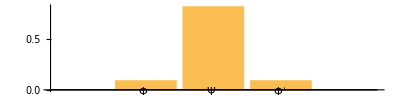

```mathematica
qmo[QuantumState[{1,3,0,ⅈ},"Bell"]]["ProbabilityPlot",AspectRatio->1/4]
```

Define a POVM measurement:

```mathematica
povm=QuantumMeasurementOperator["TetrahedronSICPOVM"]
```

QuantumMeasurementOperator[…]

```mathematica
povm[QuantumState["RandomPure"]]["Probabilities"]
```

<|𝒯_1→0.281638,𝒯_2→0.393874,𝒯_3→0.314281,𝒯_4→0.0102072|>

When QuantumMeasurementOperator acts on QuantumState, QuantumMeasurement is generated:

```mathematica
result = QuantumMeasurementOperator["X"][QuantumState[{0.2,0.6}]]
```

QuantumMeasurement[…]

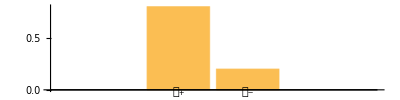

```mathematica
result["ProbabilityPlot",AspectRatio->1/4]
```

There are two ways we can perform multiqubit measurements. The first method is sequential measurement:

```mathematica
result1 = QuantumMeasurementOperator[][QuantumState["RandomPure"[2]]]
```

QuantumMeasurement[…]

```mathematica
result2 = QuantumMeasurementOperator[{2}][result1]
```

QuantumMeasurement[…]

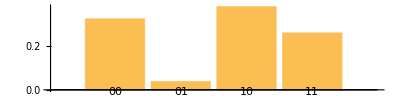

```mathematica
result2["ProbabilityPlot",AspectRatio->1/4]
```

To define the state of non-interacting subsystem or to define local operations on composite system,  QuantumTensorProduct is used. It can performs tensor product on bases, states, or operators.

Tensor product of states and bases:

```mathematica
QuantumTensorProduct[{QuantumState["0"], QuantumState["1"]}]
```

01

```mathematica
QuantumTensorProduct[{QuantumBasis["X"], QuantumBasis["Y"]}]
```

<|𝓍_+𝓎_+→(1/2 | ⅈ/2
1/2 | ⅈ/2),𝓍_+𝓎_−→(1/2 | -ⅈ/2
1/2 | -ⅈ/2),𝓍_−𝓎_+→(1/2 | ⅈ/2
-1/2 | -ⅈ/2),𝓍_−𝓎_−→(1/2 | -ⅈ/2
-1/2 | ⅈ/2)|>

Tensor product of operators (QuantumOperator or QuantumMeasurementOperator):

```mathematica
QuantumTensorProduct[QuantumOperator["Z"], QuantumOperator["Z"]]
```

QuantumOperator[…]

```mathematica
QuantumTensorProduct[
QuantumMeasurementOperator["X"], QuantumMeasurementOperator["Y"]]
```

QuantumMeasurementOperator[…]

The representation of quantum state and operator can be changed according to any basis transformation. Basis transformation is applicable to QuantumState, QuantumOperator, and QuantumMeasurementOperator as demonstrated below:

Basis change for a quantum state:

```mathematica
QuantumState[QuantumState["1"], "Y"]
```

-ⅈ/(√2)𝓎_++ⅈ/(√2)𝓎_−

Basis change for a quantum operator:

```mathematica
QuantumOperator[QuantumOperator["X"], "Y"]
```

-ⅈ𝓎_+𝓎_−+ⅈ𝓎_−𝓎_+

One can do more operations on quantum operators and the result will be a QuantumOperator:

```mathematica
op=Exp[-ⅈ ϕ/2 QuantumOperator["X"]]
```

QuantumOperator[…]

```mathematica
op==QuantumOperator["RX"[ϕ]]//FullSimplify
```

True

## Advanced quantum objects

QuantumCircuitOperator | quantum circuit as a list of quantum operations
QuantumPartialTrace | reduced state or reduced basis by tracing out subsystems
QuantumPartialTranspose | partial transposition of a quantum state or operator
QuantumDistance | distance between two quantum states
QuantumEntangledQ | check whether a quantum state is entangled
QuantumEntanglementMonotone | entanglement monotone that measures the entanglement of a quantum state
QuantumShortcut | label list of a given quantum circuit

Basic objects and operations in discrete quantum mechanics naturally lead to an application in quantum information and computation. Quantum Information is the study of information encoded in quantum systems. Meanwhile, quantum computation is the manipulation of quantum information to perform a computation.

In quantum information, it is often convenient to have a local state description of a multiqubit state. For instance, Alice and Bob shared a (possibly entangled) quantum state. But, since they are really far away from each other, they do not have access to each other state. In such scenario, Alice's description of her part of quantum state is described by a "reduced state" that can be obtained by QuantumPartialTrace operation.

Trace out the second subsystem in a two-qubit state:

```mathematica
QuantumPartialTrace[QuantumState["PsiPlus"],{2}]
```

1/2 00+1/2 11

Partial trace can also be applied to QuantumBasis:

```mathematica
QuantumPartialTrace[QuantumBasis[2,2],{2}]
```

QuantumBasis[…]

Partial transpose is an operation defined for multiple subsystems state in which only a specific subsystem is transposed. For instance, if there are two subsystems, partial transpose with respect to the first subsystem is defined by a map ρ_1⊗ρ_2→ ρ_1^T⊗ρ_2. Partial transpose operation is represented by QuantumPartialTranspose.

Example of partial transpose:

```mathematica
QuantumPartialTranspose[QuantumState["PsiPlus"],{2}]
```

1/2 0011+1/2 0101+1/2 1010+1/2 1100

Although partial transpose is not a physical operation (it does not map a density matrix to another density matrix), this operation is quite useful for detecting entanglement. In particular, it is used to compute logarithmic negativity which is commonly used metric to measure entanglement between two states. There are several other metrics to measure entanglement such as concurrence and entanglement entropy. The calculation of entanglement measure is represented by QuantumEntanglementMonotone function.

Plotting various entanglement measure for the state α00+ √(1-α^2)11

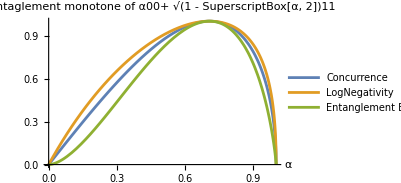

```mathematica
Plot[{
QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],"Concurrence"],
	QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],"LogNegativity"],
	QuantityMagnitude@QuantumEntanglementMonotone[QuantumState[{α,0,0,Sqrt[1-α^2]}],"EntanglementEntropy"]},{α,0,1},
PlotLabel->"Entaglement monotone of α00+ √(1 - SuperscriptBox[α, 2])11",
AxesLabel->{"α",None},PlotLegends->{"Concurrence", "LogNegativity", "Entanglement Entropy"}]
```

To know whether a state is entangled or separable without computing its measure, QuantumEntangledQ is used.

Checking whether a subsystem 1 and 3 is entangled in "W" state:

```mathematica
QuantumEntangledQ[QuantumState["W"],{{1},{3}}]
```

True

In quantum information, there exist notions of distance between quantum state such as fidelity, trace distance, Bures angle, et cetera. One may compute distance between two quantum state using various metrics by QuantumDistance:

Measuring trace distance between a pure state and a mixed state:

```mathematica
QuantumDistance[QuantumState[{{1/4,0},{0,3/4}}], QuantumState[{1,0}],"BuresAngle"]
```

π/3

Wolfram quantum framework also supports Schmidt decomposition and spectral decomposition.

Example of Schmidt decomposition:

```mathematica
state = QuantumState["PhiPlus"]["SchmidtBasis"];
state["Basis"]["Association"]//Map@Normal
state["Amplitudes"]
```

<|u_1 v_1→{{0,0},{0,1}},u_1 v_2→{{0,0},{1,0}},u_2 v_1→{{0,1},{0,0}},u_2 v_2→{{1,0},{0,0}}|>

<|u_1 v_1→1/(√2),u_1 v_2→0,u_2 v_1→0,u_2 v_2→1/(√2)|>

Example of spectral decomposition:

```mathematica
diagState=QuantumState[{{1/2,1/2},{1/2,1/2}}]["SpectralBasis"];
diagState["Amplitudes"]
```

<|s_1→1,s_2→0|>

Lastly, one may create a list of many quantum operators. A quantum circuit is represented by the symbol QuantumCircuitOperator.

Example for the construction of quantum circuit without measurement:

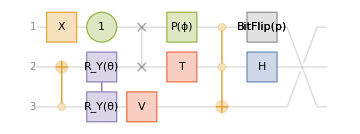

```mathematica
qc =QuantumCircuitOperator[{"X",1,"CNOT"->{3,2},{"R",θ,"YY"->{2,3}},"SWAP","SX"->3,"P"[ϕ],"T"->2,{"C","NOT"->3,{1,2}},"H"->2,"BitFlip"[p]->{1},"Braid"->{1,3}},"Parameters"->{θ,ϕ,p}];
qc["Diagram"]
```

When there is no measurement in the circuit, its action on QuantumState would return another QuantumState:

```mathematica
qc[π/3,π,π/5][]
```

QuantumState[…]

Add measurement into the circuit:

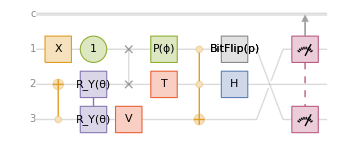

```mathematica
qc2 =qc/*{{1,3}};
qc2["Diagram"]
```

When there is measurement in the circuit, its action on QuantumState would return QuantumMeasurement:

```mathematica
N[qc2[π/3,π,π/5]][]
```

QuantumMeasurement[…]

Decomposition of CNOT:

```mathematica
qc=QuantumCircuitOperator[{"RY"[-π/2]->2,"CZ","RY"[π/2]->2}];
qc["Diagram"]
```

-Graphics-

```mathematica
QuantumOperator[qc]==QuantumOperator["CNOT"]
```

True

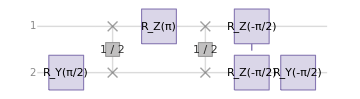

```mathematica
qc=QuantumCircuitOperator[{"RY"[π/2]->2,"RootSWAP","RZ"[π],"RootSWAP","RZ"[-π/2]->{1,2},"RY"[-π/2]->2}];
qc["Diagram"]
```

```mathematica
QuantumOperator[qc]==QuantumOperator["CNOT"]
```

True

A quantum gate for the magic basis transformation (transforming 2 qubit computational basis to the Bell basis):

```mathematica
qc=QuantumCircuitOperator["Magic"];
qc["Diagram"]
```

-Graphics-

```mathematica
qc[QuantumState["00"]]==QuantumState["PhiPlus"]
```

True

```mathematica
qc[QuantumState["10"]]==ⅈ QuantumState["PsiPlus"]
```

True

```mathematica
qc[QuantumState["01"]]==ⅈ QuantumState["PhiMinus"]
```

True

```mathematica
qc[QuantumState["11"]]== QuantumState["PsiMinus"]
```

True

More About

Related Tech Notes

Related Wolfram Education Group Courses